```mathematica
Solve[a*x^3+b*x^2+c*x+d==0/.{a->1.0,b->2,c->3,d->4},x]
```

{{x→-1.65063},{x→-0.174685-1.54687 ⅈ},{x→-0.174685+1.54687 ⅈ}}

```mathematica
Solve[a*x^3+b*x^2+c*x+d==0/.{a->1,b->2,c->3,d->4},x]
```

{{x→1/3 (-2-5^(2/3)/(-7+3 √6)^(1/3)+(5 (-7+3 √6))^(1/3))},{x→-2/3+(5^(2/3) (1+ⅈ √3))/(6 (-7+3 √6)^(1/3))-1/6 (1-ⅈ √3) (5 (-7+3 √6))^(1/3)},{x→-2/3+(5^(2/3) (1-ⅈ √3))/(6 (-7+3 √6)^(1/3))-1/6 (1+ⅈ √3) (5 (-7+3 √6))^(1/3)}}

```mathematica
NSolve[a*x^3+b*x^2+c*x+d==0/.{a->1,b->2,c->3,d->4},x]
```

{{x→-1.65063},{x→-0.174685-1.54687 ⅈ},{x→-0.174685+1.54687 ⅈ}}

```mathematica
Solve[x^5-2*x^3+x+5==0,x]
```

{{x→Root[5+#1-2 #1^3+#1^5&,1]},{x→Root[5+#1-2 #1^3+#1^5&,2]},{x→Root[5+#1-2 #1^3+#1^5&,3]},{x→Root[5+#1-2 #1^3+#1^5&,4]},{x→Root[5+#1-2 #1^3+#1^5&,5]}}

```mathematica
NSolve[x^5-2*x^3+x+5==0,x]
```

{{x→-1.65477},{x→-0.527822-1.02701 ⅈ},{x→-0.527822+1.02701 ⅈ},{x→1.35521-0.655415 ⅈ},{x→1.35521+0.655415 ⅈ}}

```mathematica
Solve[Sqrt[1+x+x^2]==2,x]
```

{{x→1/2 (-1-√13)},{x→1/2 (-1+√13)}}

```mathematica
N[%]
```

{{x→-2.30278},{x→1.30278}}

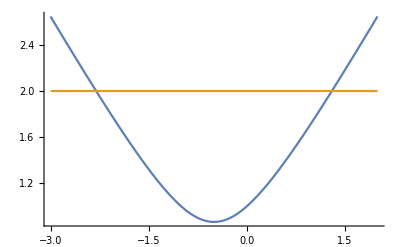

```mathematica
Plot[{Sqrt[1+x+x^2],2},{x,-3,2}]
Dynamic[MousePosition["Graphics"]]
```

```mathematica
Solve[x^(1/4)==2*x,x]
```

{{x→0},{x→1/(2 2^(1/3))}}

```mathematica
N[%]
```

{{x→0.},{x→0.39685}}

```mathematica
Solve[E^x==x^2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2 ProductLog[-1/2]},{x→-2 ProductLog[1/2]}}

```mathematica
?ProductLog
```

ProductLog[z] gives the principal solution for w in z==w e^w. 
ProductLog[k,z] gives the k^th solution.

```mathematica
NSolve[E^x==x^2,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.703467},{x→1.58805-1.54022 ⅈ}}

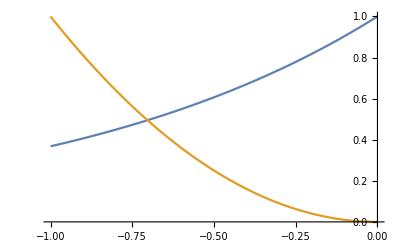

```mathematica
Plot[{E^x,x^2},{x,-1,0}]
```

```mathematica
FindRoot[E^x==x^2,{x,-0.7}]
```

{x→-0.703467}

```mathematica
Solve[Log[x]==x^3-2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-(-1)^(2/3) (1/3 ProductLog[-3/ⅇ^6])^(1/3)},{x→-(-1)^(2/3) (1/3 ProductLog[-1,-3/ⅇ^6])^(1/3)}}

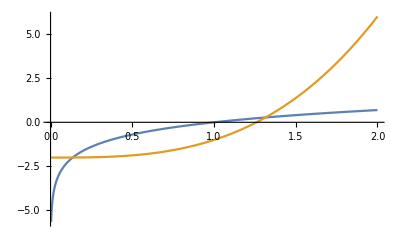

```mathematica
Plot[{Log[x],x^3-2},{x,0,2}]
```

```mathematica
FindRoot[Log[x]==x^3-2,{x,0.1}]
```

{x→0.135674}

```mathematica
FindRoot[Log[x]==x^3-2,{x,1.3}]
```

{x→1.31498}

```mathematica
Solve[{y==x+2,y==-x^2+10},{x,y}]
```

{{x→1/2 (-1-√33),y→1/2 (3-√33)},{x→1/2 (-1+√33),y→1/2 (3+√33)}}

```mathematica
NSolve[{y==x+2,y==-x^2+10},{x,y}]
```

{{x→2.37228,y→4.37228},{x→-3.37228,y→-1.37228}}

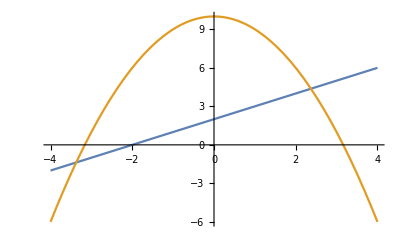

```mathematica
Plot[{x+2,-x^2+10},{x,-4,4}]
```

```mathematica
Solve[{a*x+b*y==c,d*x+e*y==f},{x,y}]
```

{{x→-(c e-b f)/(b d-a e),y→-(-c d+a f)/(b d-a e)}}

```mathematica
massaction={(1.6+x)*(3*x)^3/((1.4-x)*(2.3-x))==1.8*10^-7};
roots=Solve[massaction]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-1.6},{x→-0.00118642-0.00206073 ⅈ},{x→-0.00118642+0.00206073 ⅈ},{x→0.00237286}}

```mathematica
pCH4=1.4-x/.roots[[4]]
```

1.39763